# Automatic Determination of Logical Universality in Cellular Automaton using Rule 624 as an example

Brian J LuValle

Mentor: Nikki Sigurdson

Universality was determined in the cellular automaton rule 110 using the patterns found in gliders, In this notebook a system for automatic detection of universal glider configurations is discussed. In this notebook the logical universality of two Totalistic 4 neighbor cellular automaton rule 624 and 626 are used as examples for this system. The gliders are identified through examining a series of structures and their points with respect to each other. With these gliders, the ending points are found and the systems with common ending points are marked as intersecting. The gliders which are found stemming from these common ending points are interpreted as resulting gliders. These glider intersections are cataloged and then analyzed and combined to determine the ability of the systems to represent  the logically universal Nand Gate.

## Configuration

```mathematica
rule=18;<|"OuterTotalisticCode"->624,"Range"->2,"Colors"->2|>;
```

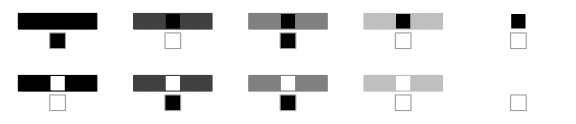
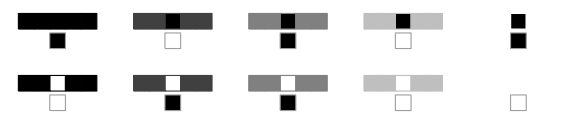

```mathematica
Row[{RulePlot[CellularAutomaton[<|"OuterTotalisticCode"->624,"Range"->2,"Colors"->2|>],ImageSize->Large],RulePlot[CellularAutomaton[<|"OuterTotalisticCode"->626,"Range"->2,"Colors"->2|>],ImageSize->Large]}]
```

Figure 1: From Left to Right : The Cellular Automaton rules 624 and 626, both have been deemed candidates for universal computation by Stephen Wolfram.

```mathematica
Row[{ArrayPlot[CellularAutomaton[<|"OuterTotalisticCode"->624,"Range"->2,"Colors"->2|>,Table[RandomInteger[],400],400],ImageSize->Large],ArrayPlot[CellularAutomaton[<|"OuterTotalisticCode"->626,"Range"->2,"Colors"->2|>,Table[RandomInteger[],400],400],ImageSize->Large]}]
```

-Graphics--Graphics-

Figure 2: From Left to Right : Cellular Automaton systems with rules 624 and 626 for random initial conditions.

## System

## Tolerances and Configuration

This system is designed so that the regions of tolerance and boundaries are configurable and adjustable for any case

```mathematica
Distance[list_]:=Sqrt[Total@Table[n^2,{n,list}]]
```

This function takes the distance {0,0} and a 2d vector of points

```mathematica
Structures[matrix_,n_]:=Table[Table[Table[Table[matrix[[r+j,k+g]],{g,-n+j,n-j}],{j,n}],{r,n+1,Length[matrix]-1-n}],{k,n+1,Length[matrix[[1]]]-1-n}]
```

This function takes all of different unbounded programs of size p

```mathematica
TriangleArrayPlot[data_]:=ArrayPlot[Table[Flatten[Append[Prepend[data[[n]],Table["",n]],Table["",n]]],{n,Length[data]}],ImageSize->Tiny]
```

This graphical function is used to display individual structures and gliders

```mathematica
GliderGraph[glider_]:=Graph[Flatten[{Table[TriangleArrayPlot[graphicalgliders[[n]]]->"interaction",{n,glider[[1]]}],Table["interaction"->TriangleArrayPlot[graphicalgliders[[n]]],{n,glider[[2]]}]}],VertexLabels->"Name",ImageSize->Medium]
```

GliderGraph displays a graph of a glider interaction

```mathematica
TriangleSimilarity[data_,key_]:=Total[Flatten[Table[Table[If[key[[c,h]]==data[[c,h]],1,0],{h,Length[data[[c]]]}],{c,Length[data]}]]]/Length[Flatten[key]]
```

This function compares the similarity of two gliders

```mathematica
ListSubtract[list1_,list2_]:=If[Length[list1]<Length[list2],Table[list1[[n]]-list2[[n]],{n,Length[list1]}],Table[list1[[n]]-list2[[n]],{n,Length[list2]}]]
```

ListSubtract subtracts two unevenly sized lists

```mathematica
GliderElement[glider_,glidersurperior_]:=Block[{glidersurperiorunusedoutptus=Flatten[Table[If[MemberQ[glider[[1]],r],{},r],{r,glidersurperior[[2]]}],1],glideruncoveredinputs=Flatten[Table[If[MemberQ[glidersurperior[[2]],j],{},j],{j,glider[[1]]}],1]},Flatten[{glideruncoveredinputs,glidersurperior[[1]]},1]->Flatten[{glidersurperiorunusedoutptus,glider[[2]]},1]]
```

GliderElement takes the combined interactions of two gliders for an output glider

```mathematica
GliderDecompose[glider_]:=Flatten[Table[Table[Table[Table[{glider[[1,r]],glider[[1,n]]}->{glider[[2,g]],glider[[2,k]]},{k,Delete[Range[Length[glider[[2]]]],g]}],{g,Length[glider[[2]]]}],{r,Delete[Range[Length[glider[[1]]]],n]}],{n,Length[glider[[1]]]}],3]
```

This function decomposes a glider into sets of two input and two output gliders

## Finding Gliders

Before gliders and their vectors can be identified, first the unique structures must be identified. A structure is a small unit of information in space time which is transmitted in a cellular automata. The wolfram classes can be correlated with the number of unique structures, Wolfram Class 4 systems like 110 have many unique structures, but not as many as Wolfram Class 3 systems such as rule 30, Wolfram Class 2 and 1 have the least unique structures. Structures are taken in the form of an initial condition and resulting generations of cells which have not been interfered with by boundary conditions.

```mathematica
structures=Structures[CellularAutomaton[rule,RandomInteger[1,200],200],5];
```

Commonest::dstlms: The requested number of elements 500 is greater than the number of distinct elements 202. Only 202 elements will be returned.

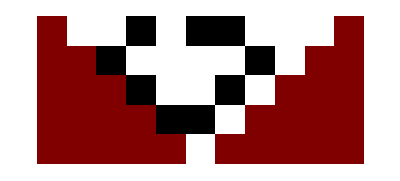

```mathematica
TriangleArrayPlot[Commonest[Flatten[structures,1],500][[25]]]
```

Figure 3: An example structure is shown above

To find gliders, the positions of the unique structures must be taken first. For a unique structure to be a glider, it must first exceed a certain number of different occurrences throughout the automaton as well as a common positions with respect to the closest one. This position with respect to each other effectively gives the gliders vector.

```mathematica
gliderpositions=Parallelize[Table[{Position[structures,n],n},{n,Commonest[Intersection[Flatten[structures,1]],500]}]];
```

Commonest::dstlms: The requested number of elements 500 is greater than the number of distinct elements 202. Only 202 elements will be returned.

```mathematica
commonalitybound=15;
```

```mathematica
glidervectors=Flatten[Table[If[Length[n[[1]]]==1,{n},{}],{n,Flatten[Table[If[Length[gliderpositions[[n,1]]]>commonalitybound,{{Flatten[Commonest[Table[If[gliderpositions[[n,1,k,1]]≠Max[Table[i[[1]],{i,gliderpositions[[n,1]]}]],{gliderpositions[[n,1,k]]-Nearest[Flatten[Table[If[gliderpositions[[n,1,k,1]]<r[[1]],{r},{}],{r,gliderpositions[[n,1]]}],1],gliderpositions[[n,1,k]]][[1]]},{}],{k,Length[gliderpositions[[n,1]]]}]],1],gliderpositions[[n,2]]}},{}],{n,Length[gliderpositions]}],1]}],1];
```

## Naming and Classification of Gliders

When the gliders are found to commonly occur next to each other and also have the same vector, there are interpreted to be the same glider.

```mathematica
commonvectorlist=Table[Flatten[Table[If[g[[1,1]]==r,{g},{}],{g,glidervectors}],1],{r,Intersection[Flatten[Table[If[Length[n[[1]]]==1,n[[1]],{}],{n,glidervectors}],1]]}];
```

```mathematica
commonvectorpositionlist=Table[Table[{Sort[Position[structures,commonvectorlist[[k,n,2]]]],commonvectorlist[[k,n,2]]},{n,Length[commonvectorlist[[k]]]}],{k,Length[commonvectorlist]}];(*a list of the common vectors and the respective positions of the gliders for which that is the most common vector*)
```

```mathematica
occurancetolerability=5;
```

```mathematica
commongliders=Flatten[Table[If[Length[n]>1,{Table[Flatten[Table[If[Length[k[[1]]]≠Length[j[[1]]],If[Max[{Length[k[[1]]],Length[j[[1]]]}]-occurancetolerability<Min[{Length[k[[1]]],Length[j[[1]]]}],{{ListSubtract[k[[1]],j[[1]]],{k[[2]],j[[2]]}}},{}],{{{k[[1]]-j[[1]]},{k[[2]],j[[2]]}}}],{k,n}],1],{j,n}]},{}],{n,commonvectorpositionlist}],1];
```

```mathematica
puritybound=0.75;
```

```mathematica
refinedcommongliders=Intersection[Table[Sort[Intersection[Flatten[j,1]]],{j,GatherBy[Intersection[Table[Sort[n[[2]]],{n,Flatten[Table[Flatten[Table[Flatten[Table[If[MemberQ[commongliders[[r,k,g,1]][[1]],{0,0}],{},If[Length[Position[commongliders[[r,k,g,1]][[1]],Commonest[commongliders[[r,k,g,1]][[1]]][[-1]]]]/Length[commongliders[[r,k,g,1]][[1]]]>puritybound,{commongliders[[r,k,g]]},{}]],{g,Length[commongliders[[r,k]]]}],1],{k,Length[commongliders[[r]]]}],1],{r,Length[commongliders]}],1](*note create a commonality bound for which if the commonality of the most common position of gliders with respect to eachtother they are considered homogenous.*)}]],#[[1]]&]}]];
```

```mathematica
finalgliders=Join[refinedcommongliders,Table[{n},{n,Complement[Table[n[[2]],{n,glidervectors}],Intersection[Flatten[refinedcommongliders,1]]]}]];
```

## Finding Collisions and Interactions

Once the gliders have been grouped and classified together, the terminations and starts of each of the gliders are taken and then analyzed to find intersecting gliders or “valence” gliders. At the point of intersection of valence gliders, a radius  is set around to discover outgoing valence gliders resulting from the interaction. If a set is not found, the collision will be marked as resulting in a null set.  With the sets of interacting gliders, combinations of those interactions are composed and cataloged.

```mathematica
catalougedgliders=Table[Table[Block[{clist={},block={}},{Table[If[r[[n,1]]≠r[[n-1,1]],{AppendTo[block,clist],clist={}},AppendTo[clist,r[[n]]]],{n,2,Length[r]}],block}[[-1]]],{r,b}],{b,Block[{catalouge=Table[Table[Sort[Position[structures,i]],{i,g}],{g,finalgliders}]},Parallelize[Table[Table[Delete[Table[{catalouge[[a,b,c]]-catalouge[[a,b,c+1]],catalouge[[a,b,c+1]]},{c,Length[catalouge[[a,b]]]-1}],1],{b,Length[catalouge[[a]]]}],{a,Length[catalouge]}]]]}];
```

```mathematica
gliderterminations=Table[Table[Flatten[Table[If[Length[catalougedgliders[[a,b,c]]]>0,{catalougedgliders[[a,b,c,-1,2]]},{}],{c,Length[catalougedgliders[[a,b]]]}],1],{b,Length[catalougedgliders[[a]]]}],{a,Length[catalougedgliders]}](*the list of all of the positions at which the gliders stop*);
```

```mathematica
trianglesimilaritybound=0.75
```

0.75

```mathematica
replacementrules=Block[{uniquegliders=Flatten[Table[Block[{list=Table[r[[2]],{r,g}]},If[Mean[Mean[Table[TriangleSimilarity[r,k],{r,list},{k,list}]]]<trianglesimilaritybound,{Table[g[[n,3]],{n,Length[g]}]},Table[g[[n,3]],{n,Length[g]}]]],{g,GatherBy[Table[Flatten[{glidervectors[[g]],g},1],{g,Length[glidervectors]}],#[[1]]&]}],1]},Flatten[Table[If[Length[uniquegliders[[g]]]>1,Table[uniquegliders[[g,r]]->g,{r,Length[uniquegliders[[g]]]}],uniquegliders[[g]]->g],{g,Length[uniquegliders]}],1]];
```

```mathematica
graphicalgliders=Table[If[Length[n[[-1]]]==2,n[[-1,2]],n[[-1]]],{n,Flatten[Table[Block[{list=Table[r[[2]],{r,g}]},If[Mean[Mean[Table[TriangleSimilarity[r,k],{r,list},{k,list}]]]<trianglesimilaritybound,{Table[glidervectors[[g[[n,3]]]],{n,Length[g]}]},Table[glidervectors[[g[[n,3]]]],{n,Length[g]}]]],{g,GatherBy[Table[Flatten[{glidervectors[[g]],g},1],{g,Length[glidervectors]}],#[[1]]&]}],1]}];
```

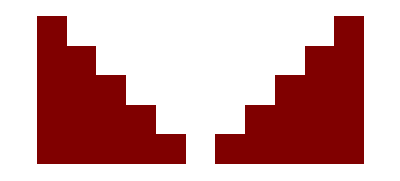
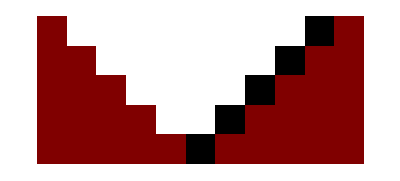
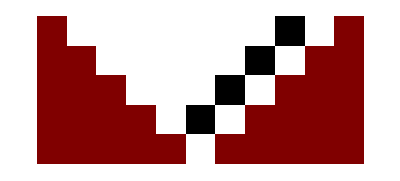
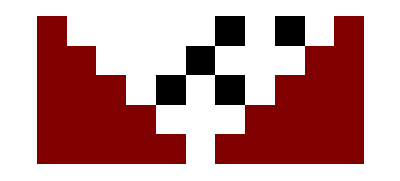
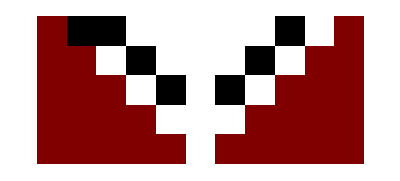
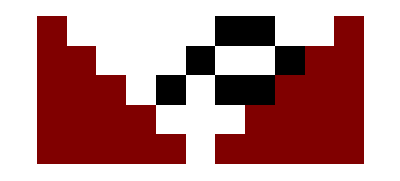
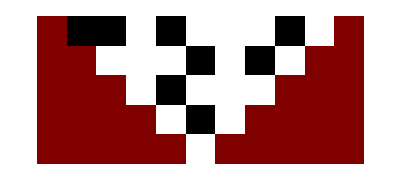
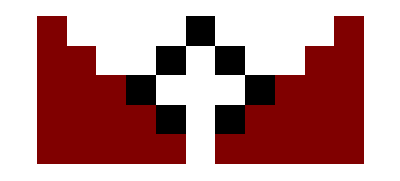

```mathematica
Table[TriangleArrayPlot[n],{n,graphicalgliders}]
```

Figure 4: The set of the “valence” gliders i.e the ones which interact with other gliders to form different gliders.

```mathematica
interactionlimit=2;
```

```mathematica
interactinggliders=Flatten[Parallelize[Table[Block[{sys4=Flatten[Block[{sys3=Flatten[Table[Block[{sys2=Flatten[Table[Block[{sys=Intersection[Block[{data={a}},{Table[Table[Flatten[Table[If[TrueQ[Abs[Distance[gliderterminations[[a,b,c]]-gliderterminations[[j,h,i]]]]<interactionlimit],AppendTo[data,j],{}],{i,Length[gliderterminations[[j,h]]]}],1],{h,Length[gliderterminations[[j]]]}],{j,Length[gliderterminations]}],data}[[-1]]]]},If[Length[sys]>1,{{sys/.replacementrules,gliderterminations[[a,b,c]]}},{}]],{c,Length[gliderterminations[[a,b]]]}],1]},If[Length[sys2]>0,{sys2},{}]],{b,Length[gliderterminations[[a]]]}],1]},If[Length[sys3]>0,{sys3},{}]],1]},If[Length[sys4]>0,{sys4},{}]],{a,Length[gliderterminations]}]],1];
```

```mathematica
trianglesimilaritybound=0.75;
```

```mathematica
gliderbegginings=Table[Table[Flatten[Table[If[Length[catalougedgliders[[a,b,c]]]>0,{catalougedgliders[[a,b,c,1,2]]},{}],{c,Length[catalougedgliders[[a,b]]]}],1],{b,Length[catalougedgliders[[a]]]}],{a,Length[catalougedgliders]}];
```

```mathematica
exitinggliders=Parallelize[Table[Table[Table[{Intersection[Block[{data={a}},{Table[Table[Flatten[Table[If[TrueQ[Abs[Distance[gliderbegginings[[a,b,c]]-gliderbegginings[[j,h,i]]]]<interactionlimit],AppendTo[data,j],{}],{i,Length[gliderbegginings[[j,h]]]}],1],{h,Length[gliderbegginings[[j]]]}],{j,Length[gliderbegginings]}],data/.replacementrules}[[-1]]]],gliderbegginings[[a,b,c]]},{c,Length[gliderbegginings[[a,b]]]}],{b,Length[gliderbegginings[[a]]]}],{a,Length[gliderterminations]}]];
```

```mathematica
gliderpatterns=Intersection[Flatten[Parallelize[Table[Table[Table[Block[{clist={}},
{Table[Table[Table[If[Abs[Distance[interactinggliders[[a,b,c,2]]-exitinggliders[[j,h,k,2]]]]<interactionlimit,AppendTo[clist,exitinggliders[[j,h,k,1]]],{}],{k,Length[exitinggliders[[j,h]]]}],{h,Length[exitinggliders[[j]]]}],{j,Length[exitinggliders]}];interactinggliders[[a,b,c,1]]->Intersection[Flatten[clist,1]]}],{c,Length[interactinggliders[[a,b]]]}],{b,Length[interactinggliders[[a]]]}],{a,Length[interactinggliders]}]],3]]/.replacementrules;
```

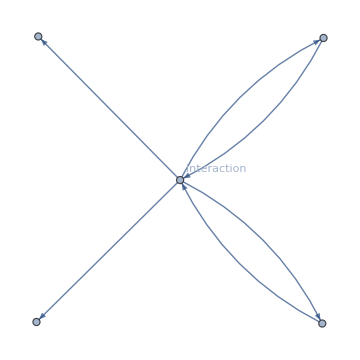
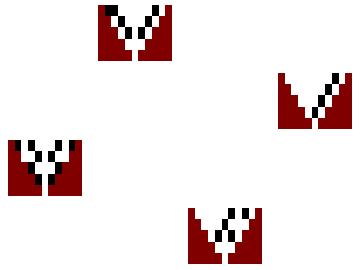
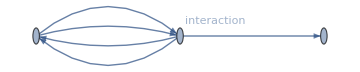
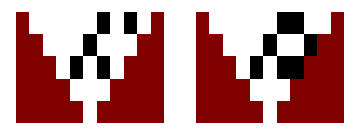
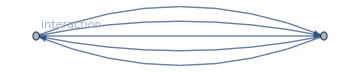
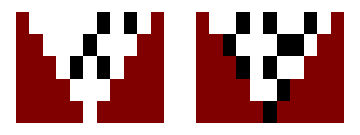
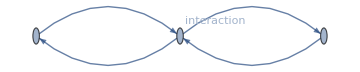
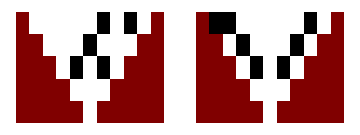
{-Graphics-
-Graphics-,-Graphics-,-Graphics-,-Graphics-
-Graphics-,-Graphics-
-Graphics-,-Graphics-
-Graphics-,-Graphics-
-Graphics-,-Graphics-
-Graphics-,-Graphics-,-Graphics-
-Graphics-,-Graphics-
-Graphics-,-Graphics-
-Graphics-,-Graphics-
-Graphics-,-Graphics-
-Graphics-,-Graphics-
-Graphics-,-Graphics-
-Graphics-,-Graphics-
-Graphics-,-Graphics-
-Graphics-,-Graphics-
-Graphics-,-Graphics-
-Graphics-}

```mathematica
Table[GliderGraph[n],{n,Take[gliderpatterns,20]}]
```

Figure 5: The list of glider interactions shown in graphical form.

## Minimization of the glider systems and finding universal behavior

In order for a system to be defined as logically universal, first it must be proven computationally equivalent to already known logically universal systems. One such already known example is the Nand Gate, below translated into glider form, 4 different gliders are used, two per binary state. To compare the glider interactions to this nand gate, two elements of the inputs of the glider systems are selected and two outputs of the same glider system are taken for all gliders, this set of combinations is then examined to see whether it matches the NAND gate pattern.

nand={{b,c}→{a,d},{a,b}→{a,d},{d,b}→{a,d},{a,c}→{a,d},{c,d}→{a,d},{a,d}→{b,c}}

Figure 6: The simplest glider based NAND gate is shown above, The values 0 and 1 can be substituted for the Gliders A and D, and C and B respectively.

```mathematica
gliderprograms=Intersection[Flatten[Table[Table[Table[gliderpatterns[[a,b,c]],{c,Length[gliderpatterns[[a,b]]]}],{b,Length[gliderpatterns[[a]]]}],{a,Length[gliderpatterns]}]]];
```

```mathematica
inputs=Table[{j,Flatten[Table[If[MemberQ[a[[1]],j],{a},{}],{a,gliderpatterns}],1]},{j,gliderprograms}];
```

```mathematica
outputs=Table[{j,Flatten[Table[If[MemberQ[a[[2]],j],{a},{}],{a,gliderpatterns}],1]},{j,gliderprograms}];
```

```mathematica
timefeature=200;
```

This error is typical during operation for less complex systems.

```mathematica
sizedinteractions=If[Length[gliderpatterns]<250,
Flatten[Parallelize[Table[Table[GliderDecompose[GliderElement[a,b]],{a,gliderpatterns}],{b,gliderpatterns}]]],
Block[{qdata=Intersection[Flatten[Table[Take[Sort[Intersection[Table[GliderElement[gliderpatterns[[a]],gliderpatterns[[b]]],{a,Length[gliderpatterns]}]],Length[#1[[1]]]>Length[#2[[1]]]&],250],{b,Length[gliderpatterns]}],1]]},Flatten[Table[GliderDecompose[qdata[[RandomInteger[{0,Length[qdata]}]]]],{r,timefeature}]]]];
```

Take::take: Cannot take positions 1 through 250 in ….

General::stop: Further output of Take::take will be suppressed during this calculation.

```mathematica
programcount=10;
```

```mathematica
commonestprograms=Union[Commonest[Flatten[Table[sizedinteractions[[r,1]],{r,Length[sizedinteractions]}]],programcount],Commonest[Flatten[Table[sizedinteractions[[r,2]],{r,Length[sizedinteractions]}]],programcount]];
```

## Output

The output is shown below, it either outputs a True or a False depending on the configuration of the gliders being used.

```mathematica
Block[{var={}},{MemberQ[Flatten[Parallelize[Table[Table[Table[Table[If[MemberQ[Table[MemberQ[sizedinteractions,g],{g,
{{commonestprograms[[b]],commonestprograms[[c]]}->{commonestprograms[[a]],commonestprograms[[d]]},{commonestprograms[[a]],commonestprograms[[b]]}->{commonestprograms[[a]],commonestprograms[[d]]},{commonestprograms[[d]],commonestprograms[[b]]}->{commonestprograms[[a]],commonestprograms[[d]]},{commonestprograms[[a]],commonestprograms[[c]]}->{commonestprograms[[a]],commonestprograms[[d]]},{commonestprograms[[c]],commonestprograms[[d]]}->{commonestprograms[[a]],commonestprograms[[d]]},{commonestprograms[[a]],commonestprograms[[d]]}->{commonestprograms[[b]],commonestprograms[[c]]}}
}],False],{False,Print[False]}[[1]],{True,Print[True]}[[1]]],{a,Delete[Range[Length[commonestprograms]],{{d},{c},{b}}]}],{b,Delete[Range[Length[commonestprograms]],{{d},{c}}]}],{c,Delete[Range[Length[commonestprograms]],d]}],{d,Length[commonestprograms]}]],3],True],var}[[2]]]
```

$Aborted

## Conclusions

From this paper, it has been seen that the program has the capability to identify systems of gliders and their respective collisions, with this it has been possible to identify the presence of universal logical gates within the system. However, this tool does not have the capability to find complete universality and the tool does not have the capability to find gliders outside of a preselected image. Also, this system lacks the flexibility to find larger gliders automatically, for that the system needs to be configured. Another problem that exists is the calculation time. This I hope can be solved with better glider finding algorithms and better glider comparison algorithms.